## Examples of the Lagrangian

Scott A. Hughes, 18 October 2010

Begin by picking an initial velocity, give value of gravitational acceleration, mass, time that ball is in flight.

```mathematica
vx = 5;
vy0 = 5;
g = 10;
m=1;
T = 2vy0/g;
```

Equation describing height above ground as a function of time t.

```mathematica
y0[t_] = vy0 t - (1/2)g t^2;
```

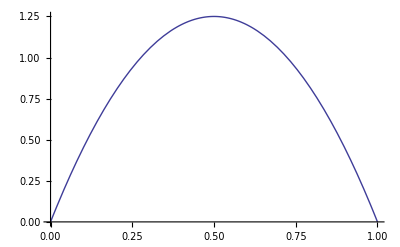

```mathematica
Plot[y0[t],{t,0,T}]
```

A modified version of this equation, designed to see what happens as we deviate from the correct solution.  Notice that it is designed so that the initial (t = 0) and final (t = T) points coincide with the correct solution.

```mathematica
y1[t_] = y0[t](1 + ϵ Sin[20π t/T]);
```

The y-component of velocity for this modified trajectory.

```mathematica
vy1[t_] = D[y1[t],t];
```

The kinetic and potential energies corresponding to this trajectory.

```mathematica
K1[t_] = (m/2)(vx^2+vy1[t]^2);
V1[t_] = m g y1[t];
```

And the Lagrangian.

```mathematica
L1[t_] = Simplify[K1[t]-V1[t]]
```

1/2 (25+100 (-1+t) t (1+ϵ Sin[20 π t])+(-100 π (-1+t) t ϵ Cos[20 π t]+(5-10 t) (1+ϵ Sin[20 π t]))^2)

Before computing the action, let's see what this trajectory looks like:

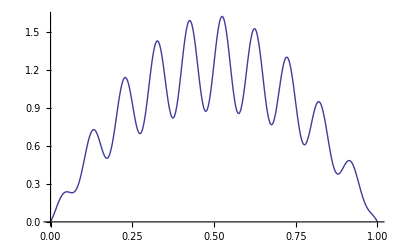

```mathematica
Plot[y1[t]/.ϵ->0.3,{t,0,T}]
```

OK, now compute the action for this Lagrangian.

```mathematica
S1[ϵ_] = Simplify[Expand[Integrate[L1[t],{t,0,T}]]]
```

25/3+(25/12-1/(128 π^2)+(250 π^2)/3) ϵ^2

Notice that this is that this is smallest for ϵ = 0!  For any non-zero value of ϵ, the action is larger than S1[0].

Just for fun, let's try a different modified trajectory: This just shifts the whole thing a bit, again making sure that the end points are in the correct place.

```mathematica
y2[t_] = y0[t](1 + ϵ t(T-t));
```

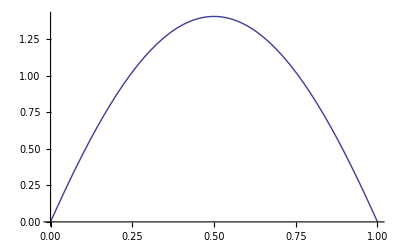

```mathematica
Plot[y2[t]/.ϵ->0.5, {t,0,T}]
```

```mathematica
vy2[t_] = D[y2[t],t];
```

```mathematica
K2[t_] = (m/2)(vx^2+vy2[t]^2);
V2[t_] = m g y2[t];
```

```mathematica
L2[t_] = Simplify[K2[t]-V2[t]]
```

25/2 (1+4 (-1+t) t (1-(-1+t) t ϵ)+(1-2 t)^2 (1+2 t ϵ-2 t^2 ϵ)^2)

```mathematica
S2[ϵ_] = Integrate[L2[t],{t,0,T}]
```

25/3+(5 ϵ^2)/21

Once again, the action is smallest when ϵ = 0; any non-zero ϵ pushes us away from that minimum value.